```mathematica
L1= 1.7; (*m*) (*Пассивное волокно на входе в усилитель*)
L2=3.5;(*m*)(*Активное волокно*)
L3=2.;(*m*)(*Пассивное волокно на выходе усилителя*)
L=L1+L2+L3; (*m*) (*Длина всего оптического тракта*)
α0dB=0.2/10^3;(*dB/m*)(*потери в пассивном волокне*)
α1dB=0.08;(*dB/m*)(*потери в активном волокне*)(*значение для YbEr 6000 ppm*)
α0=Log[10^(α0dB/10)];(*1/м*)
α1=Log[10^(α1dB/10)];(*1/м*)
```

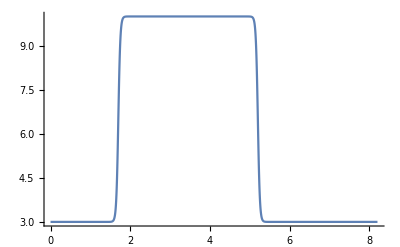

```mathematica
Plot[(10-3)(Tanh[20(z-L1)]+1)(-Tanh[20(z-L2-L1)]+1)/4+3,{z,0,L+1},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
Clear[α];
α[z_,L1_,L2_]:=(α1-α0)(Tanh[20(z-L1)]+1)(-Tanh[20(z-L2-L1)]+1)/4+α0;
```

```mathematica
α[1,L1,L2]
α[2.5,L1,L2]
α[4,L1,L2]
α1
α0
```

0.0000460517

0.0184207

0.0184207

0.0184207

0.0000460517

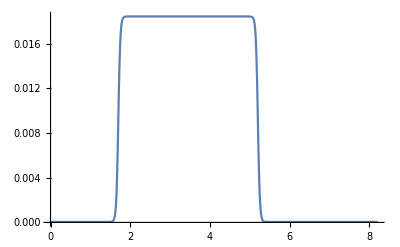

```mathematica
Plot[α[z,L1,L2],{z,0,L+1},PlotRange->All,AxesOrigin->{0,0},ImageSize->Full]
```

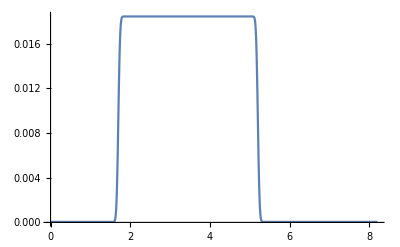

```mathematica
α[z_,L1_,L2_]:=(α1-α0)(Erf[20(z-L1)]+1)(-Erf[20(z-L2-L1)]+1)/4+α0;
Plot[α[z,L1,L2],{z,0,L+1},PlotRange->All,AxesOrigin->{0,0},ImageSize->Full]
```

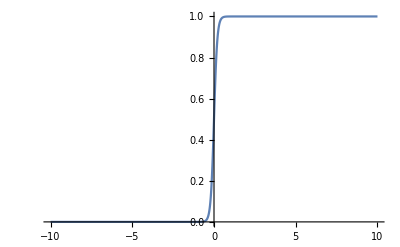

```mathematica
Plot[(Tanh[5 z]+1)/2,{z,-10,10},PlotRange->All]
```